```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\刘兴瑞\Documents\Visual Studio 2015\Projects\pipedata\pipedata

```mathematica
datar=Import["r.csv"];
datac=Import["c.csv"];
datav=Import["v.csv"];
datad=Import["d.csv"];
```

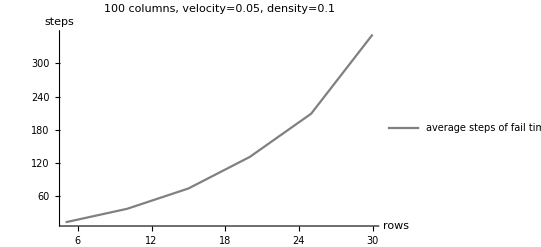

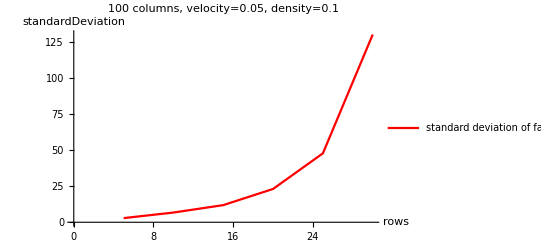

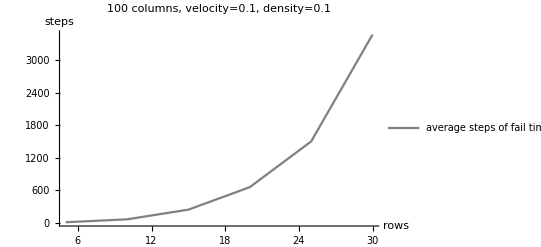

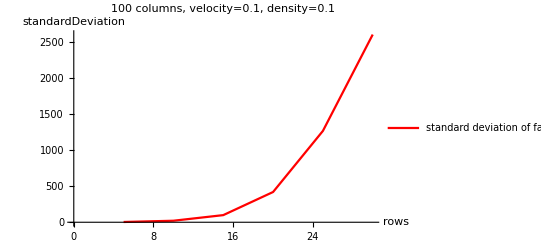

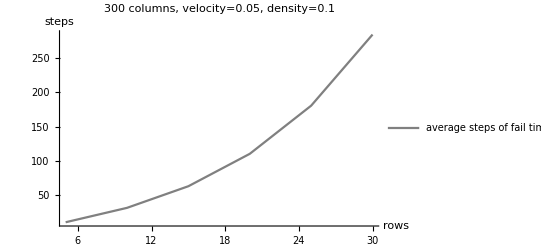

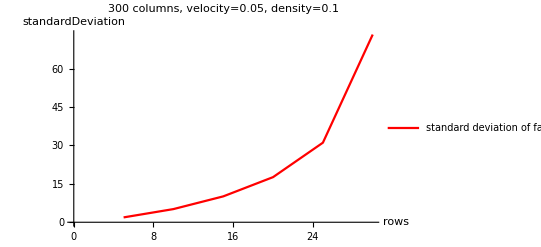

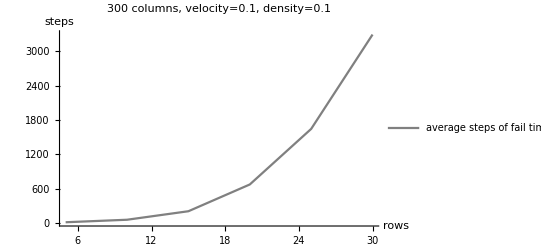

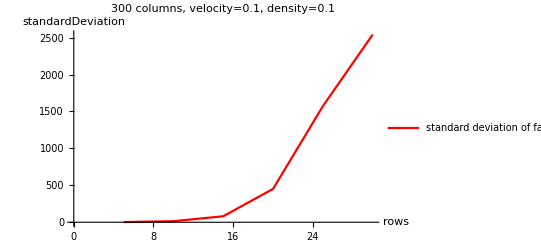

```mathematica
Do[average={};standardDeviation={};Do[average=Append[average,{(j+1)*5,datar[[2+6*i+j,5]]}];standardDeviation=Append[standardDeviation,{(j+1)*5,datar[[2+6*i+j,6]]^0.5}];
,{j,0,5}];
name=Switch[i,0,"100 columns, velocity=0.05, density=0.1",1,"100 columns, velocity=0.1, density=0.1 ",2,
"300 columns, velocity=0.05, density=0.1 ",3,"300 columns, velocity=0.1, density=0.1"];
pa=ListLinePlot[average,PlotStyle->Gray,PlotLegends->{"average steps of fail times for pipes"}];
pvc=ListLinePlot[standardDeviation,PlotStyle->Red,AxesOrigin->{0,0},AxesLabel->{"rows","standardDeviation"},PlotLabel->name,PlotLegends->{"standard deviation of fail times for pipes"}];
Print[Show[pa,AxesOrigin->{0,0},PlotRange->Automatic,AxesLabel->{"rows","steps"},PlotLabel->name]];
Print[pvc];
,{i,0,3}]
```

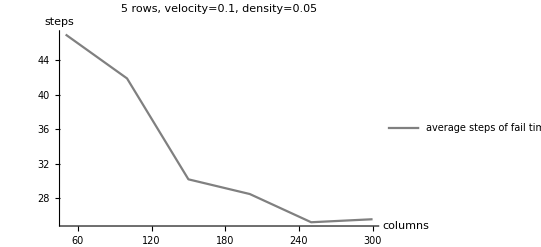

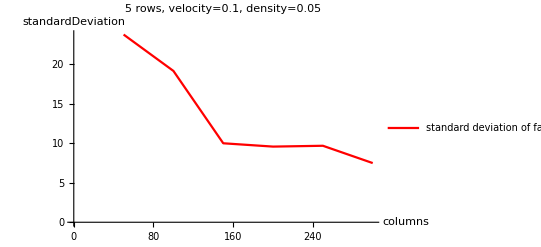

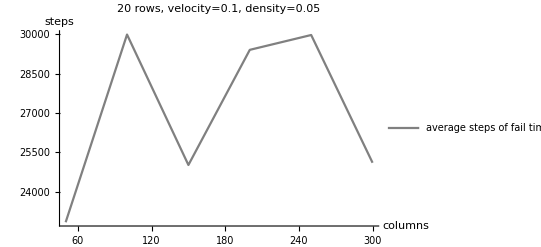

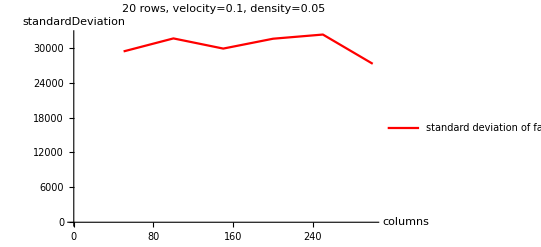

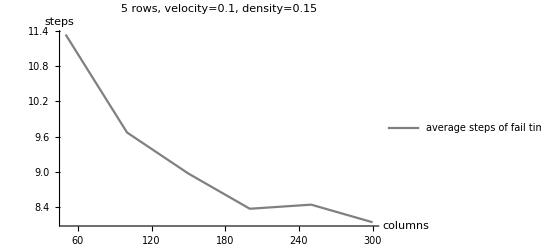

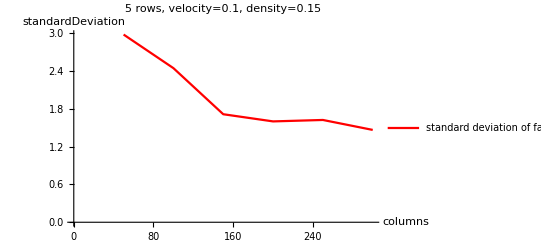

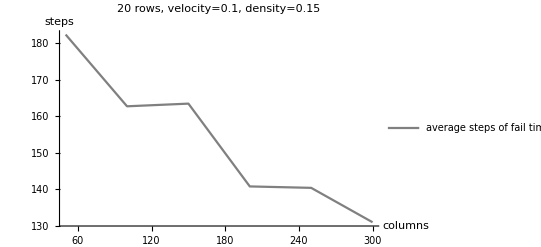

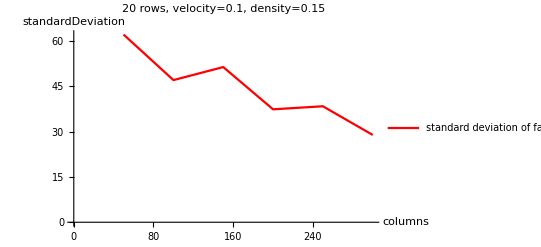

```mathematica
Do[average={};standardDeviation={};Do[average=Append[average,{(j+1)*50,datac[[2+6*i+j,5]]}];standardDeviation=Append[standardDeviation,{(j+1)*50,datac[[2+6*i+j,6]]^0.5}];
,{j,0,5}];
name=Switch[i,0,"5 rows, velocity=0.1, density=0.05",1,"20 rows, velocity=0.1, density=0.05 ",2,
"5 rows, velocity=0.1, density=0.15 ",3,"20 rows, velocity=0.1, density=0.15"];

pa=ListLinePlot[average,PlotStyle->Gray,PlotLegends->{"average steps of fail times for pipes"}];
pvc=ListLinePlot[standardDeviation,PlotStyle->Red,AxesOrigin->{0,0},AxesLabel->{"columns","standardDeviation"},PlotLabel->name,PlotLegends->{"standard deviation of fail times for pipes"}];
Print[Show[pa,AxesOrigin->{0,0},PlotRange->Automatic,AxesLabel->{"columns","steps"},PlotLabel->name]];
Print[pvc];
,{i,0,3}]
```

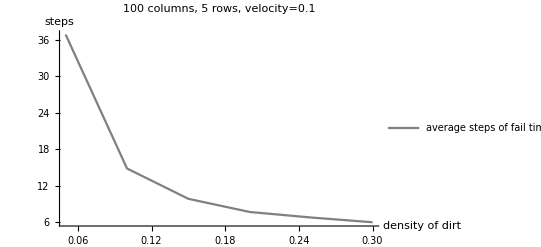

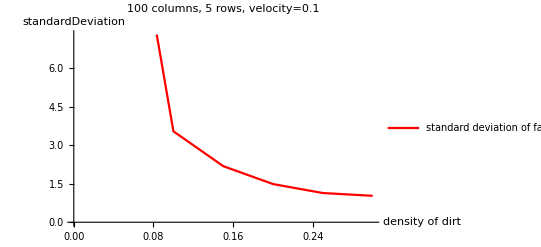

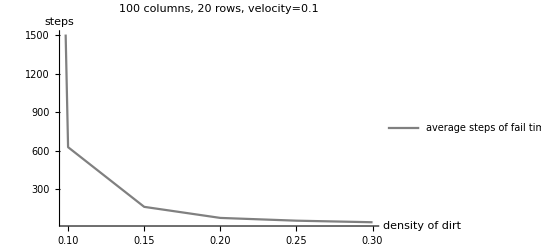

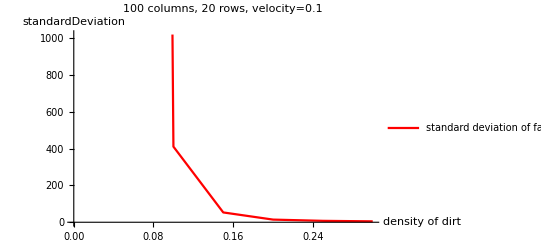

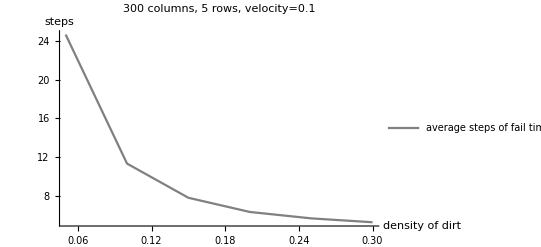

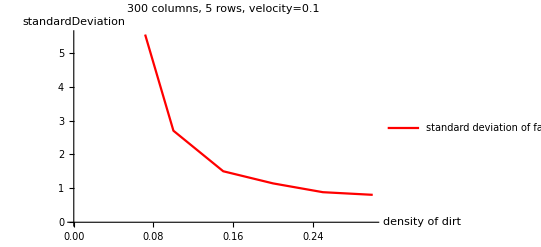

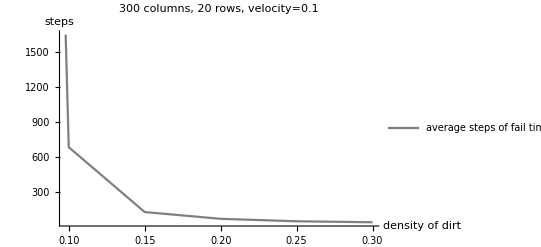

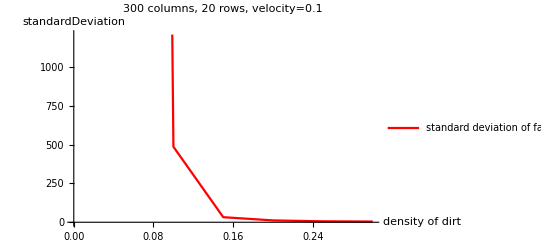

```mathematica
Do[average={};standardDeviation={};Do[average=Append[average,{(j+1)*0.05,datad[[2+6*i+j,5]]}];standardDeviation=Append[standardDeviation,{(j+1)*0.05,datad[[2+6*i+j,6]]^0.5}];
,{j,0,5}];
name=Switch[i,0,"100 columns, 5 rows, velocity=0.1",1,"100 columns, 20 rows, velocity=0.1 ",2,
"300 columns, 5 rows, velocity=0.1 ",3,"300 columns, 20 rows, velocity=0.1"];

pa=ListLinePlot[average,PlotStyle->Gray,PlotLegends->{"average steps of fail times for pipes"}];
pvc=ListLinePlot[standardDeviation,PlotStyle->Red,AxesOrigin->{0,0},AxesLabel->{"density of dirt","standardDeviation"},PlotLabel->name,PlotLegends->{"standard deviation of fail times for pipes"}];
Print[Show[pa,AxesOrigin->{0,0},PlotRange->Automatic,AxesLabel->{"density of dirt","steps"},PlotLabel->name]];
Print[pvc];
,{i,0,3}]
```

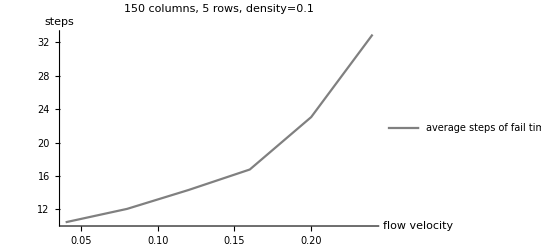

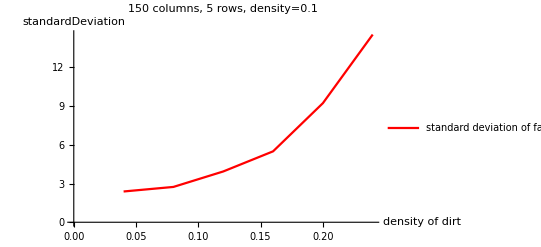

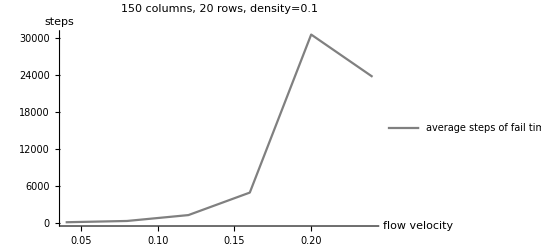

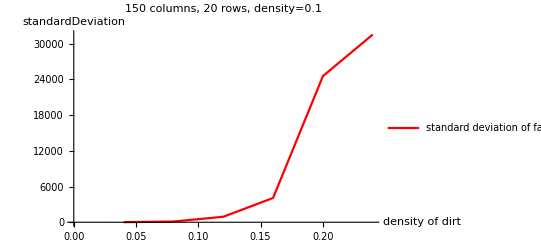

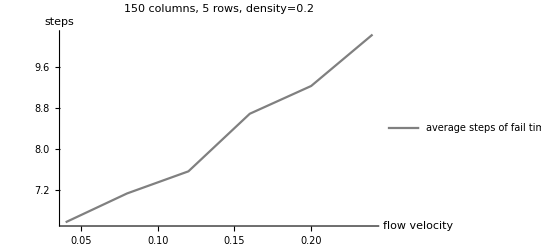

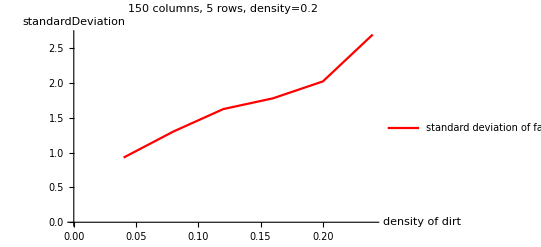

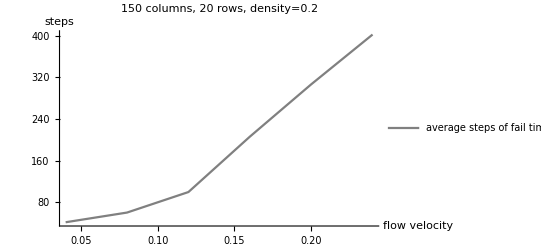

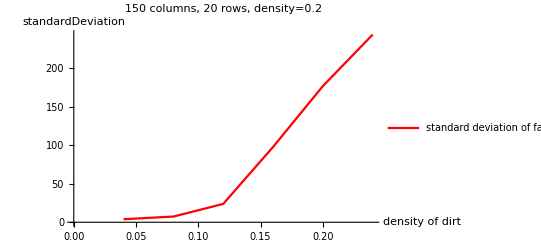

```mathematica
Do[average={};standardDeviation={};Do[average=Append[average,{(j+1)*0.04,datav[[2+6*i+j,5]]}];standardDeviation=Append[standardDeviation,{(j+1)*0.04,datav[[2+6*i+j,6]]^0.5}];
,{j,0,5}];
name=Switch[i,0,"150 columns, 5 rows, density=0.1",1,"150 columns, 20 rows, density=0.1 ",2,
"150 columns, 5 rows, density=0.2 ",3,"150 columns, 20 rows, density=0.2"];

pa=ListLinePlot[average,PlotStyle->Gray,PlotLegends->{"average steps of fail times for pipes"}];
pvc=ListLinePlot[standardDeviation,PlotStyle->Red,AxesOrigin->{0,0},AxesLabel->{"density of dirt","standardDeviation"},PlotLabel->name,PlotLegends->{"standard deviation of fail times for pipes"}];
Print[Show[pa,AxesOrigin->{0,0},PlotRange->Automatic,AxesLabel->{"flow velocity","steps"},PlotLabel->name]];
Print[pvc];
,{i,0,3}]
```